```mathematica
Σ11[t_,U_,ω_]:=U/2+(U^2 t)/(4 √(4 t^2+2 t U))(1/(ω-(t+√(4 t^2+2 t U)))+1/(ω+(t+√(4 t^2+2 t U))))
Σ12[t_,U_,ω_]:=(U^2 t)/(4 √(4 t^2+2 t U))(1/(ω-(t+√(4 t^2+2 t U)))-1/(ω+(t+√(4 t^2+2 t U))))
Opp11[t_,U_,ω_]:=U+(U^2 t)/(2 √(4 t^2+2 t U))(1/(ω-(√(4 t^2+2 t U)))-1/(ω+(√(4 t^2+2 t U))))
Opp12[t_,U_,ω_]:=(U^2 t)/(2 √(4 t^2+2 t U))(1/(ω-(√(4 t^2+2 t U)))-1/(ω+(√(4 t^2+2 t U))))
Σvv[t_,U_,ω_]:=Σ11[t,U,ω]+Σ12[t,U,ω] 
Σcc[t_,U_,ω_]:=Σ11[t,U,ω]-Σ12[t,U,ω]  
dΣvv[t_,U_,ω_]:=-((t U^2)/(4 √(4 t^2+2 t U)))((1/((-t-√(4 t^2+2t U)+ω)^2)-1/((t+√(4 t^2+2 t U)+ω)^2))+ (1/((-t-√(4 t^2+2 t U)+ω)^2)+1/((t+√(4 t^2+2 t U)+ω)^2)))
dΣcc[t_,U_,ω_]:=-((t U^2)/(4 √(4 t^2+2 t U)))(- (1/((-t-√(4 t^2+2 t U)+ω)^2)-1/((t+√(4 t^2+2 t U)+ω)^2))+ (1/((-t-√(4 t^2+2 t U)+ω)^2)+1/((t+√(4 t^2+2 t U)+ω)^2)))

ϵv[t_,U_]:=-t+1/(1-dΣvv[t,U,-t])Σvv[t,U,-t]
ϵc[t_,U_]:=t+1/(1-dΣcc[t,U,t])Σcc[t,U,t]
ϵvppdyn[t_,U_]:=-(-8 √2 t^2-4 √2 t U-2 U √(t (2 t+U))+2 √(32 t^4+32 t^3 U+8 t^2 U^2+16 t^3 (2 t+U)-8 t^2 U (2 t+U)+t U^2 (2 t+U)+32 √2 t^3 √(t (2 t+U))+8 √2 t^2 U √(t (2 t+U))))/(8 √(t (2 t+U)))
ϵcppdyn[t_,U_]:=1/(8 √(t (2 t+U)))(-8 √2 t^2-4 √2 t U+2 U √(t (2 t+U))+2 √(32 t^4+32 t^3 U+8 t^2 U^2+16 t^3 (2 t+U)+8 t^2 U (2 t+U)+t U^2 (2 t+U)+32 √2 t^3 √(t (2 t+U))+24 √2 t^2 U √(t (2 t+U))+8 √2 t U^2 √(t (2 t+U))))
Δϵppl[t_,U_]:=(2 (-16 t^2-5 t U+8 √2 t √(t (2 t+U))+√2 U √(t (2 t+U))))/U
ΔϵgwL[t_,U_]:=(64 t^3+96 t^2 U+26 t U^2-32 t U √(t (t+U))-4 U^2 √(t (t+U)))/(32 t^2+32 t U-U^2)
```

```mathematica
ℰ23as[t_,U_,Δv_]:=2/3 (U+ √(12 t^2+U^2+3 Δv^2) Cos[1/3 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))]])
ℰ22as[t_,U_,Δv_]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Cos[1/3 (π+ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])])
ℰ21as=0;
ℰ20as[t_,U_,Δv_]:=2/3 (U- √(12 t^2+U^2+3 Δv^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/((12 t^2+U^2+3 Δv^2)^(3/2))])])
ωEAexcas[t_,U_,Δv_]:=1/6 (2 U-3 t √(4+Δv^2/t^2)+4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])])
ωEIexcas[t_,U_,Δv_]:=1/6 (4 U+3 t √(4+Δv^2/t^2)-4 t √((12 t^2+U^2+3 Δv^2)/t^2) Sin[1/6 (π+2 ArcCos[-(U (18 t^2+U^2-9 Δv^2))/(t^3 ((12 t^2+U^2+3 Δv^2)/t^2)^(3/2))])])
excas1[t_,U_,Δv_]:= - ℰ20as[t,U,Δv]
excas2[t_,U_,Δv_]:= ℰ22as[t,U,Δv]- ℰ20as[t,U,Δv]
Egap[t_,U_,Δv_]     :=ωEAexcas[t,U,Δv]-ωEIexcas[t,U,Δv]
Eb1exc[t_,U_,Δv_]:=Egap[t,U,Δv]-excas1[t,U,Δv]
Eb2exc[t_,U_,Δv_]:=Egap[t,U,Δv]-excas2[t,U,Δv]
```

```mathematica
Htpp[Δϵ_,t_,U_]:=({{Δϵ-U/2, -(U t)/(2t+U)}, {(U t)/(2t+U), -(Δϵ-U/2)}})
Hspp[Δϵ_,t_,U_]:=({{Δϵ+U/2, (U t)/(2t+U)}, {-(U t)/(2t+U), -(Δϵ+U/2)}})
```

```mathematica
vtppgz[t_,U_]:=(√((8 t^2-U^2) (8 t^2+4 t U-U^2)))/(2 (2 t+U))
vsppgz[t_,U_]:=(√((8 t^2+4 t U+U^2) (8 t^2+8 t U+U^2)))/(2 (2 t+U))
```

```mathematica
vtppstat[t_,U_]:=(t √(t^3 (2 t+U) (128 t^4+32 √2 t^2 U √(t (2 t+U))+U^3 (U-2 √2 √(t (2 t+U)))-4 t U^2 (U+2 √2 √(t (2 t+U)))+32 t^3 (3 U+2 √2 √(t (2 t+U))))))/((t (2 t+U))^(3/2) (2 t+√2 √(t (2 t+U))))
vsppstat[t_,U_]:=1/((t (2 t+U))^(3/2) (2 t+√2 √(t (2 t+U))))t √(t^2 (2 t+U) (128 t^5+2 U^4 (U+√2 √(t (2 t+U)))+32 t^4 (7 U+2 √2 √(t (2 t+U)))+32 t^3 U (5 U+3 √2 √(t (2 t+U)))+4 t^2 U^2 (17 U+14 √2 √(t (2 t+U)))+t U^3 (17 U+18 √2 √(t (2 t+U)))))
```

```mathematica
vtppdyn[t_,U_]:=1/(2 (2 t+U))(√(128 t^4+176 t^3 U+82 t^2 U^2+18 t U^3+(3 U^4)/2+32 √2 t^3 √(t (2 t+U))+48 √2 t^2 U √(t (2 t+U))+28 √2 t U^2 √(t (2 t+U))+6 √2 U^3 √(t (2 t+U))-8 t^2 U √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-8 t U^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-2 U^3 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-16 √2 t^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-16 √2 t U √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-4 √2 U^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-8 t^2 U √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-8 t U^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-2 U^3 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-16 √2 t^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-16 √2 t U √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-4 √2 U^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+8 t^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+8 t U √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+2 U^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)))
vsppdyn[t_,U_]:=1/(2 (2 t+U))(√(128 t^4+176 t^3 U+82 t^2 U^2+18 t U^3+(3 U^4)/2+32 √2 t^3 √(t (2 t+U))+16 √2 t^2 U √(t (2 t+U))-4 √2 t U^2 √(t (2 t+U))-2 √2 U^3 √(t (2 t+U))+8 t^2 U √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)+8 t U^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)+2 U^3 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-16 √2 t^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-16 √2 t U √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)-4 √2 U^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)+8 t^2 U √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+8 t U^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+2 U^3 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-16 √2 t^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-16 √2 t U √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)-4 √2 U^2 √(t (2 t+U)) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+8 t^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+8 t U √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)+2 U^2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2) √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2)))
```

```mathematica
vtQPpp[t_,U_]:=(√(320 t^4+t^3 (352 U-64 √(16 t^2+U^2))+4 t U^2 (7 U-8 √(16 t^2+U^2))+16 t^2 U (8 U-5 √(16 t^2+U^2))+U^3 (5 U-4 √(16 t^2+U^2))))/(2 (2 t+U))
vsQPpp[t_,U_]:=(√(320 t^4+12 t U^3+16 t^2 U (4 U-3 √(16 t^2+U^2))+32 t^3 (9 U-2 √(16 t^2+U^2))+U^3 (5 U+4 √(16 t^2+U^2))))/(2 (2 t+U))
```

```mathematica
vt1pp[t_,U_]:=(t √(t^3 (2 t+U) (320 t^4+U^3 (U-4 √2 √(t (2 t+U)))-4 t U^2 (U+4 √2 √(t (2 t+U)))+16 t^2 U (3 U+4 √2 √(t (2 t+U)))+32 t^3 (9 U+4 √2 √(t (2 t+U))))))/(2 (t (2 t+U))^(3/2) (t+√2 √(t (2 t+U))))
```

```mathematica
vs1pp[t_,U_]:=1/(2 (t (2 t+U))^(3/2) (t+√2 √(t (2 t+U))))t √(t^2 (2 t+U) (320 t^5+4 U^4 (2 U+√2 √(t (2 t+U)))+32 t^4 (19 U+4 √2 √(t (2 t+U)))+16 t^3 U (31 U+12 √2 √(t (2 t+U)))+4 t^2 U^2 (59 U+28 √2 √(t (2 t+U)))+t U^3 (65 U+36 √2 √(t (2 t+U)))))
```

```mathematica
vt1ppl[t_,U_]:=1/(2 U (2 t+U))(√(32768 t^6+4 t U^4 (19 U-64 √2 √(t (2 t+U)))+U^5 (U-8 √2 √(t (2 t+U)))-2048 t^5 (-27 U+8 √2 √(t (2 t+U)))-608 t^3 U^2 (-17 U+20 √2 √(t (2 t+U)))-16 t^2 U^3 (-87 U+170 √2 √(t (2 t+U)))-64 t^4 U (-549 U+368 √2 √(t (2 t+U)))))
vs1ppl[t_,U_]:=1/(2 U (2 t+U))(√(32768 t^6+16 t^2 U^3 (51 U-134 √2 √(t (2 t+U)))-2048 t^5 (-27 U+8 √2 √(t (2 t+U)))+U^5 (U+8 √2 √(t (2 t+U)))-4 t U^4 (U+16 √2 √(t (2 t+U)))-32 t^3 U^2 (-281 U+364 √2 √(t (2 t+U)))-64 t^4 U (-533 U+368 √2 √(t (2 t+U)))))
```

```mathematica
Series[vt1pp[t,U],{U,0,4},Assumptions->t>0]//FullSimplify
```

2 t-U/2+(5 U^2)/(48 t)-(13 U^3)/(576 t^2)-(7 U^4)/(27648 t^3)+O[U]^5

```mathematica
With[{Δv=0},ListPlot[
{Table[Flatten[{U,excas1[1,U,Δv]}],{U,0,20,0.1}],
Table[Flatten[{U,excas2[1,U,Δv]}],{U,0,20,0.1}],
Table[Flatten[{U,vt1pp[1,U]}],{U,0,20,0.1}],
Table[Flatten[{U,vs1pp[1,U]}],{U,0,20,0.1}]},
Joined->True,PlotLegends->{"excas1","excas2","vt1pp","vs1pp"},Frame->True,FrameLabel->{"U","Binding Energies"}]]
```

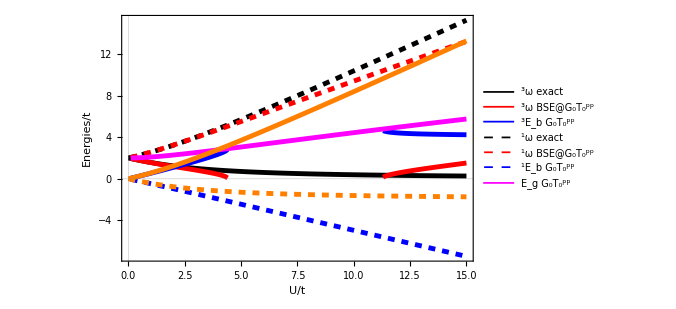

```mathematica
TripletSinguletT=With[{Δv=0},ListPlot[
{Table[Flatten[{U,excas1[1,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,vt1ppl[1,U]}],{U,0,15,0.1}],
Table[Flatten[{U,(Δϵppl[1,U]-vt1ppl[1,U])}],{U,0,15,0.1}],
Table[Flatten[{U,excas2[1,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,vs1ppl[1,U]}],{U,0,15,0.1}],
Table[Flatten[{U,(Δϵppl[1,U]-vs1ppl[1,U])}],{U,0,15,0.1}],
Table[Flatten[{U,Δϵppl[1,U]}],{U,0,15,0.1}],
Table[Flatten[{U,Eb1exc[1,U,0.0]}],{U,0,15,0.1}],
Table[Flatten[{U,Eb2exc[1,U,0.0]}],{U,0,15,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0T_0^pp","^3E_b G_0T_0^pp","^1ω exact","^1ω BSE@G_0T_0^pp","^1E_b G_0T_0^pp"," E_g G_0T_0^pp"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Red,Thickness[0.007]},{Blue,Thickness[0.007]},{Dashed,Black,Thickness[0.007]},{Dashed,Red,Thickness[0.007]},{Dashed,Blue,Thickness[0.007]},{Magenta,Thickness[0.007]},{Orange,Thickness[0.007]},{Dashed,Orange,Thickness[0.007]}}]]//Quiet
```

```mathematica
Export["Excitations_neutres_GAP_Eb_Opp.pdf",TripletSinguletT];
```

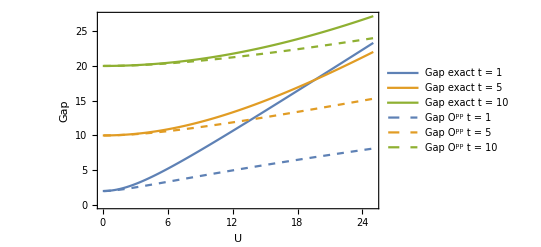

```mathematica
With[{Δv=0},ListPlot[
{Table[Flatten[{U,Egap[1,U,Δv]}],{U,0,25,0.1}],
Table[Flatten[{U,Egap[5,U,Δv]}],{U,0,25,0.1}],
Table[Flatten[{U,Egap[10,U,Δv]}],{U,0,25,0.1}],
Table[Flatten[{U,Δϵppl[1,U]}],{U,0,25,0.1}],
Table[Flatten[{U,Δϵppl[5,U]}],{U,0,25,0.1}],
Table[Flatten[{U,Δϵppl[10,U]}],{U,0,25,0.1}]},
Joined->True,PlotLegends->{"Gap exact t = 1","Gap exact t = 5","Gap exact t = 10","Gap O^pp t = 1","Gap O^pp t = 5","Gap O^pp t = 10"},Frame->True,FrameLabel->{"U","Gap"},PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],{Dashed,RGBColor[0.368417, 0.506779, 0.709798]},{Dashed,RGBColor[0.880722, 0.611041, 0.142051]},{Dashed,RGBColor[0.560181, 0.691569, 0.194885]}}
]]
```

```mathematica
Δϵppstat[t_,U_]:=2*t+(U^2*t)/(Sqrt[4 t^2+2*t*U]*(2t+Sqrt[4 t^2+2*t*U]))
Δϵppdyn[t_,U_]:=1/4 (-4 √2 √(t (2 t+U))+2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t-U/2+√(4 t^2+2 t U))^2)+2 √((2 t U^2)/(√(4 t^2+2 t U))+(2 t+U/2+√(4 t^2+2 t U))^2))
ΔeQP[t_,U_]:=-2t+Sqrt[16 t^2+U^2];
```

```mathematica
Eigenvalues[Hspp[Δϵppstat[t,U],t,U]] //FullSimplify;
```

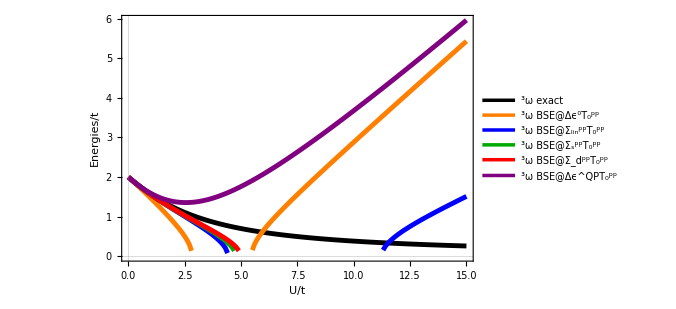

```mathematica
exctriplet=With[{t=1,Δv=0.000000},ListPlot[
{Table[Flatten[{U,excas1[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,vtppgz[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vt1ppl[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vtppstat[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vtppdyn[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vtQPpp[t,U]}],{U,0,15,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@Δϵ^0T_0^pp","^3ω BSE@Σ_lin^ppT_0^pp","^3ω BSE@Σ_s^ppT_0^pp","^3ω BSE@Σ_d^ppT_0^pp","^3ω BSE@Δϵ^QPT_0^pp"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]}, {Purple,Thickness[0.007]}}
]]//Quiet
```

```mathematica
Export["BSEGT_dim_sym_triplet.pdf",exctriplet]
```

BSEGT_dim_sym_triplet.pdf

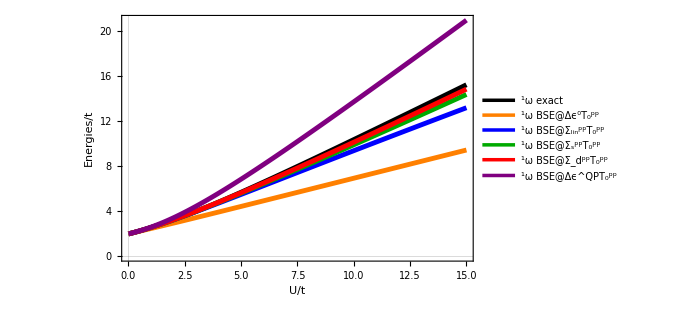

```mathematica
excsinglet=With[{t=1,Δv=0.000000},ListPlot[
{Table[Flatten[{U,excas2[t,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,vsppgz[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vs1ppl[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vsppstat[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vsppdyn[t,U]}],{U,0,15,0.1}],
Table[Flatten[{U,vsQPpp[t,U]}],{U,0,15,0.1}]},
Joined->True,PlotLegends->{"^1ω exact","^1ω BSE@Δϵ^0T_0^pp","^1ω BSE@Σ_lin^ppT_0^pp","^1ω BSE@Σ_s^ppT_0^pp","^1ω BSE@Σ_d^ppT_0^pp","^1ω BSE@Δϵ^QPT_0^pp"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20],FrameStyle->Directive[Black,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Black,Thickness[0.007]},{Orange,Thickness[0.007]},{Blue,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Red,Thickness[0.007]}, {Purple,Thickness[0.007]}}
]]//Quiet
```

```mathematica
Export["BSEGT_dim_sym_singulet.pdf",excsinglet]
```

BSEGT_dim_sym_singulet.pdf

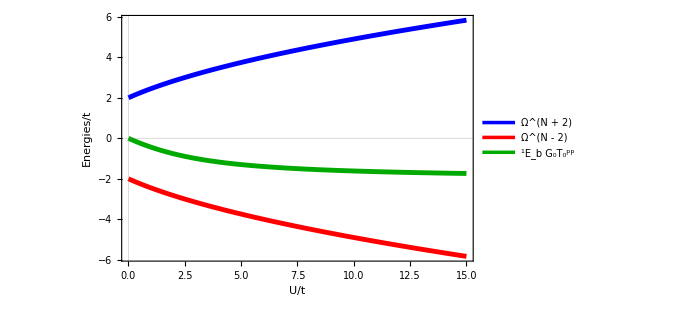

```mathematica
polesTpp=With[{t=N[1.0,150]},ListPlot[
{Table[Flatten[{U,√(4 t^2+2 t U)}],{U,0,15,0.1}],
Table[Flatten[{U,-√(4 t^2+2 t U)}],{U,0,15,0.1}],
Table[Flatten[{U,Eb2exc[1,U,0.0]}],{U,0,15,0.1}]},
Joined->True,PlotLegends->{"Ω^(N + 2)","Ω^(N - 2)","^1E_b G_0T_0^pp"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Blue,Thickness[0.007]},{Red,Thickness[0.007]},{Darker[Green],Thickness[0.007]}}]] //Quiet
```

```mathematica
Export["polesTppG0.pdf",polesTpp]
```

polesTppG0.pdf

```mathematica
Gold=RGBColor[1.0,0.843,0.0];
```

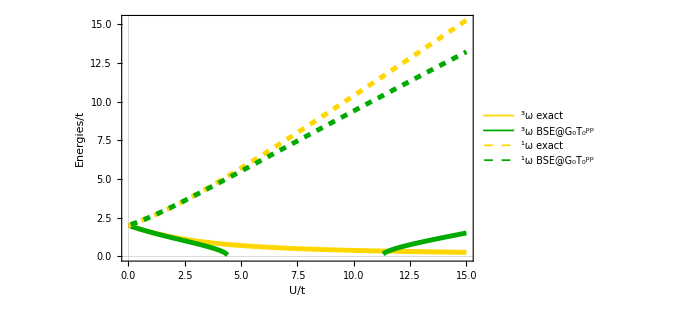

```mathematica
TripletSinguletT=With[{Δv=0},ListPlot[
{Table[Flatten[{U,excas1[1,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,vt1ppl[1,U]}],{U,0,15,0.1}],
Table[Flatten[{U,excas2[1,U,Δv]}],{U,0,15,0.1}],
Table[Flatten[{U,vs1ppl[1,U]}],{U,0,15,0.1}]},
Joined->True,PlotLegends->{"^3ω exact","^3ω BSE@G_0T_0^pp","^1ω exact","^1ω BSE@G_0T_0^pp"},Frame->True,FrameLabel->{"U/t","Energies/t"},LabelStyle->Directive[FontFamily->"Arial",White,FontSize->20],FrameStyle->Directive[White,Thick],ImageSize->500,PlotTheme->"Scientific",PlotStyle->{{Gold,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Dashed,Gold,Thickness[0.007]},{Dashed,Darker[Green],Thickness[0.007]}}]]//Quiet
```